# Fits to Brody distribution, and calculations for density of states

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
bins=Table[x,{x,0,5,0.2}];
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
Ewindowsize=30.0;
```

## Run1

```mathematica
rundata1=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run1/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
40			60

LobattoPoints		NumChannels	Order
64			60		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
50.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff1-Ewindowsize<#<Ecutoff1-1.&;
curvestemp1=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run1/AdiabaticCurves.dat"]];
Curves1=Table[Table[{curvestemp1[[1,i]],curvestemp1[[j,i]]},{i,1,Length[curvestemp1[[1]]]}],{j,2,Length[curvestemp1]}];
Evals1=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run1/Eigenvals.dat"]];
Ecutoff1=Evals1[[4]]
Evals1=Sort[Drop[Evals1,1;;4]];
eValsBound1 = Sort[Select[Evals1,SampleRange]]
```

-117.564

{-147.377,-146.742,-146.696,-146.36,-145.411,-144.061,-143.88,-143.376,-142.744,-142.602,-142.245,-141.472,-140.733,-140.529,-140.352,-139.715,-139.051,-138.857,-138.534,-138.168,-137.767,-137.461,-136.292,-135.917,-135.641,-135.537,-135.116,-134.95,-134.367,-133.555,-133.225,-133.194,-132.443,-132.198,-131.792,-131.661,-131.399,-130.951,-130.735,-130.115,-129.634,-129.387,-128.798,-128.435,-128.258,-128.126,-128.043,-127.892,-127.551,-126.892,-126.794,-126.518,-126.472,-125.813,-125.696,-125.444,-125.299,-125.059,-124.843,-124.513,-124.148,-123.943,-123.778,-123.209,-122.658,-122.488,-122.318,-121.749,-121.457,-121.355,-121.251,-121.169,-121.042,-120.757,-120.673,-120.462,-120.21,-119.889,-119.783,-119.487,-119.304,-118.983,-118.942,-118.687,-118.576}

```mathematica
Length[eValsBound1]
```

85

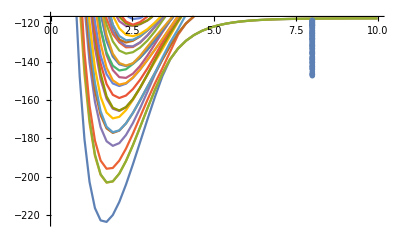

```mathematica
pcurves1=ListPlot[Curves1,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp1[[2]]],Ecutoff1+1}];
penergies1=ListPlot[Table[{8,eValsBound1[[i]]},{i,1,Length[eValsBound1]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves1,penergies1]
```

```mathematica
Es1=Table[eValsBound1[[i+1]]-eValsBound1[[i]],{i,1,Length[eValsBound1]-1}];
eTrim1= Select[Es1,#>0.0000001&];
avg1 = Mean[eTrim1];
eTrim1 = eTrim1/avg1;
(*Sort[eTrim1];*)
Length[Es1];
Length[eTrim1];
ρ1=1/avg1;
EspaceBin1=BinCounts[eTrim1,{bins}];
NormBrodyBinCs1=Table[EspaceBin1[[i]]/Total[EspaceBin1]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist1 = Table[{bFit[[i]],NormBrodyBinCs1[[i]]},{i,1,Length[bFit]}]
phist1=ListPlot[brodyPdist1,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars1 = FindFit[brodyPdist1,{PBrody[s,w],w>0,w<1},{w},s]
pfit1=Plot[PBrody[s,w/.pars1],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.238095},{0.3,0.77381},{0.5,0.833333},{0.7,0.595238},{0.9,0.77381},{1.1,0.416667},{1.3,0.119048},{1.5,0.119048},{1.7,0.297619},{1.9,0.416667},{2.1,0.119048},{2.3,0.119048},{2.5,0.},{2.7,0.0595238},{2.9,0.},{3.1,0.},{3.3,0.},{3.5,0.0595238},{3.7,0.},{3.9,0.0595238},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.484436}

```mathematica
ρ1
```

2.91652

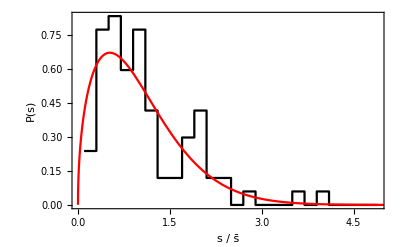

```mathematica
Show[phist1,pfit1,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run2

```mathematica
rundata2=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run2/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
40			60

LobattoPoints		NumChannels	Order
64			60		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
50.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		1		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff2-Ewindowsize<#<Ecutoff2-1&
curvestemp2=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run2/AdiabaticCurves.dat"]];
Curves2=Table[Table[{curvestemp2[[1,i]],curvestemp2[[j,i]]},{i,1,Length[curvestemp2[[1]]]}],{j,2,Length[curvestemp2]}];
Evals2=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run2/Eigenvals.dat"]];
Ecutoff2=Evals2[[4]]
Evals2=Sort[Drop[Evals2,1;;4]];
eValsBound2 = Sort[Select[Evals2,SampleRange]]
```

Ecutoff2-Ewindowsize<#1<Ecutoff2-1&

-117.564

{-147.193,-147.049,-146.756,-146.511,-146.406,-146.116,-146.092,-145.273,-144.918,-144.43,-143.825,-143.729,-143.346,-142.673,-142.32,-142.117,-141.483,-140.631,-140.546,-140.437,-139.9,-139.611,-139.406,-138.856,-138.586,-138.58,-138.17,-138.035,-137.258,-136.986,-136.391,-135.818,-135.672,-135.517,-135.047,-134.816,-134.478,-134.038,-133.376,-133.221,-133.086,-132.75,-132.58,-132.526,-132.465,-131.953,-131.89,-131.687,-131.464,-131.092,-130.592,-130.141,-129.502,-129.17,-128.996,-128.854,-128.33,-128.013,-127.891,-127.842,-127.524,-127.474,-126.971,-126.759,-126.509,-126.468,-126.354,-126.03,-125.605,-125.272,-125.115,-124.74,-124.365,-124.065,-123.622,-123.43,-123.164,-123.06,-122.93,-122.856,-122.609,-122.404,-122.332,-122.125,-121.861,-121.75,-121.475,-121.291,-120.941,-120.93,-120.552,-120.544,-120.239,-120.044,-119.906,-119.858,-119.614,-119.565,-119.354,-118.861,-118.676}

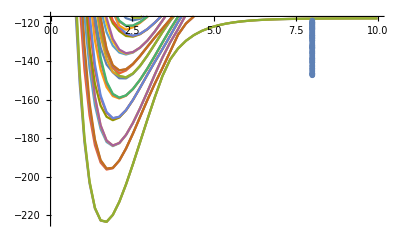

```mathematica
pcurves2=ListPlot[Curves2,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp2[[2]]],Ecutoff2+1}];
penergies2=ListPlot[Table[{8,eValsBound2[[i]]},{i,1,Length[eValsBound2]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves2,penergies2]
```

```mathematica
Es2=Table[eValsBound2[[i+1]]-eValsBound2[[i]],{i,1,Length[eValsBound2]-1}];
eTrim2 = Select[Es2,#>0.0000001&];
avg2 = Mean[eTrim2];
eTrim2 = eTrim2/avg2;
(*Sort[eTrim2];*)
Length[Es2];
Length[eTrim2];
ρ2=1/avg2;
EspaceBin2=BinCounts[eTrim2,{bins}];
NormBrodyBinCs2=Table[EspaceBin2[[i]]/Total[EspaceBin2]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist2 = Table[{bFit[[i]],NormBrodyBinCs2[[i]]},{i,1,Length[bFit]}]
phist2=ListPlot[brodyPdist2,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars2 = FindFit[brodyPdist2,{PBrody[s,w],w>0,w<1},{w},s]
pfit2=Plot[PBrody[s,w/.pars2],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.5},{0.3,0.5},{0.5,0.65},{0.7,0.65},{0.9,0.5},{1.1,0.6},{1.3,0.4},{1.5,0.25},{1.7,0.3},{1.9,0.15},{2.1,0.15},{2.3,0.2},{2.5,0.},{2.7,0.05},{2.9,0.1},{3.1,0.},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.449483}

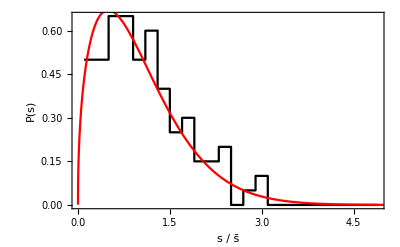

```mathematica
Show[phist2,pfit2,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run3

```mathematica
rundata3=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run3/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
80			60

LobattoPoints		NumChannels	Order
64			120		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
50.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff3-Ewindowsize<#<Ecutoff3-1&
curvestemp3=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run3/AdiabaticCurves.dat"]];
Curves3=Table[Table[{curvestemp3[[1,i]],curvestemp3[[j,i]]},{i,1,Length[curvestemp3[[1]]]}],{j,2,Length[curvestemp3]}];
Evals3=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run3/Eigenvals.dat"]];
Ecutoff3=Evals3[[4]]
Evals3=Sort[Drop[Evals3,1;;4]];
eValsBound3 = Sort[Select[Evals3,SampleRange]]
```

Ecutoff3-Ewindowsize<#1<Ecutoff3-1&

-117.564

{-147.377,-147.193,-147.049,-146.756,-146.742,-146.696,-146.511,-146.406,-146.36,-146.116,-146.092,-145.411,-145.273,-144.918,-144.43,-144.061,-143.88,-143.825,-143.729,-143.376,-143.346,-142.744,-142.673,-142.602,-142.32,-142.245,-142.117,-141.483,-141.472,-140.733,-140.631,-140.546,-140.529,-140.437,-140.352,-139.9,-139.715,-139.611,-139.406,-139.051,-138.857,-138.856,-138.586,-138.58,-138.534,-138.17,-138.168,-138.035,-137.767,-137.461,-137.258,-136.986,-136.392,-136.292,-135.917,-135.818,-135.672,-135.641,-135.537,-135.517,-135.116,-135.047,-134.95,-134.816,-134.478,-134.367,-134.038,-133.555,-133.376,-133.225,-133.221,-133.194,-133.086,-132.75,-132.58,-132.526,-132.466,-132.443,-132.198,-131.953,-131.89,-131.792,-131.687,-131.661,-131.464,-131.399,-131.092,-130.951,-130.735,-130.592,-130.141,-130.115,-129.634,-129.502,-129.387,-129.17,-128.996,-128.855,-128.798,-128.435,-128.33,-128.258,-128.126,-128.043,-128.013,-127.892,-127.892,-127.842,-127.551,-127.524,-127.474,-126.972,-126.892,-126.793,-126.759,-126.518,-126.51,-126.472,-126.468,-126.354,-126.031,-125.813,-125.696,-125.605,-125.444,-125.299,-125.272,-125.115,-125.059,-124.843,-124.74,-124.513,-124.365,-124.147,-124.065,-123.943,-123.778,-123.622,-123.43,-123.209,-123.164,-123.06,-122.93,-122.856,-122.657,-122.609,-122.488,-122.405,-122.332,-122.318,-122.126,-121.861,-121.75,-121.749,-121.476,-121.457,-121.355,-121.291,-121.251,-121.169,-121.042,-120.942,-120.93,-120.756,-120.672,-120.553,-120.544,-120.462,-120.239,-120.209,-120.045,-119.906,-119.889,-119.858,-119.783,-119.615,-119.565,-119.487,-119.355,-119.303,-118.983,-118.942,-118.861,-118.687,-118.676,-118.576}

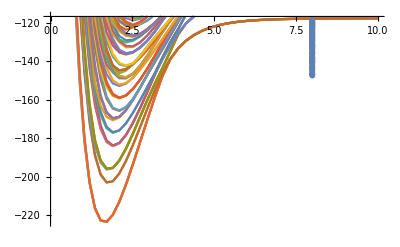

```mathematica
pcurves3=ListPlot[Curves3,Joined->True,PlotRange->{Min[curvestemp3[[2]]],Ecutoff3+1}];
penergies3=ListPlot[Table[{8,eValsBound3[[i]]},{i,1,Length[eValsBound3]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves3,penergies3]
```

```mathematica
Es3=Table[eValsBound3[[i+1]]-eValsBound3[[i]],{i,1,Length[eValsBound3]-1}];
eTrim3 = Select[Es3,#>0.0000001&];
avg3 = Mean[eTrim3];
eTrim3 = eTrim3/avg3;
Sort[eTrim3];
Length[Es3];
Length[eTrim3];
ρ3=1/avg3;
EspaceBin3=BinCounts[eTrim3,{bins}];
NormBrodyBinCs3=Table[EspaceBin3[[i]]/Total[EspaceBin3]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist3 = Table[{bFit[[i]],NormBrodyBinCs3[[i]]},{i,1,Length[bFit]}]
phist3=ListPlot[brodyPdist3,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->{Blue}];
pars3 = FindFit[brodyPdist3,{PBrody[s,w],w>0,w<1},{w},s]
pfit3=Plot[PBrody[s,w/.pars3],{s,0,5},PlotRange->All,PlotStyle->{Green}];
```

{{0.1,0.810811},{0.3,0.486486},{0.5,0.648649},{0.7,0.72973},{0.9,0.486486},{1.1,0.405405},{1.3,0.324324},{1.5,0.189189},{1.7,0.135135},{1.9,0.135135},{2.1,0.135135},{2.3,0.162162},{2.5,0.0540541},{2.7,0.},{2.9,0.0540541},{3.1,0.0810811},{3.3,0.027027},{3.5,0.},{3.7,0.},{3.9,0.0540541},{4.1,0.027027},{4.3,0.027027},{4.5,0.},{4.7,0.027027},{4.9,0.}}

{w→0.148993}

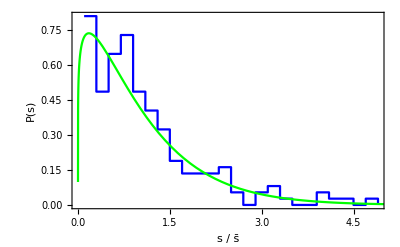

```mathematica
pall3=Show[phist3,pfit3,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

##### Analysis so far

Runs 1 and 2 have taken advantage of a possible symmetry by further reducing the coordinate space.  If my guess is right, then the density of states for run3 should be roughly twice that of run 1 and 2 since I expect both “even and odd” states about phi = π/4 to be present in run 3, but only even states in run1 and odd states in run2

```mathematica
ρ1
ρ2
ρ3
```

2.91652

3.50669

6.42326

```mathematica
ρ1+ρ2
```

6.4232

Further, I expect that if these states (even and odd) do not couple since the Hamiltonian is symmetric about ϕ=π/4, then overlaying these two distributions will result in a distribution similar to that of run3

```mathematica
eValsBoundCombined =Sort[ Flatten[{eValsBound1,eValsBound2}]]
EsCombined=Table[eValsBoundCombined[[i+1]]-eValsBoundCombined[[i]],{i,1,Length[eValsBoundCombined]-1}];
eTrimCombined = Select[EsCombined,#>0.0000001&];
avgCombined = Mean[eTrimCombined];
eTrimCombined = eTrimCombined/avgCombined;
(*Sort[eTrimCombined];*)
Length[eTrimCombined];
ρCombined=1/avgCombined;
EspaceBinCombined=BinCounts[eTrimCombined,{bins}];
NormBrodyBinCsCombined=Table[EspaceBinCombined[[i]]/Total[EspaceBinCombined]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdistCombined = Table[{bFit[[i]],NormBrodyBinCsCombined[[i]]},{i,1,Length[bFit]}]
phistCombined=ListPlot[brodyPdistCombined,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->{Black,Dashed}];
parsCombined = FindFit[brodyPdistCombined,{PBrody[s,w],w>0,w<1},{w},s]
pfitCombined=Plot[PBrody[s,w/.parsCombined],{s,0,5},PlotRange->All,PlotStyle->{Red,Dashed}];
```

{-147.377,-147.193,-147.049,-146.756,-146.742,-146.696,-146.511,-146.406,-146.36,-146.116,-146.092,-145.411,-145.273,-144.918,-144.43,-144.061,-143.88,-143.825,-143.729,-143.376,-143.346,-142.744,-142.673,-142.602,-142.32,-142.245,-142.117,-141.483,-141.472,-140.733,-140.631,-140.546,-140.529,-140.437,-140.352,-139.9,-139.715,-139.611,-139.406,-139.051,-138.857,-138.856,-138.586,-138.58,-138.534,-138.17,-138.168,-138.035,-137.767,-137.461,-137.258,-136.986,-136.391,-136.292,-135.917,-135.818,-135.672,-135.641,-135.537,-135.517,-135.116,-135.047,-134.95,-134.816,-134.478,-134.367,-134.038,-133.555,-133.376,-133.225,-133.221,-133.194,-133.086,-132.75,-132.58,-132.526,-132.465,-132.443,-132.198,-131.953,-131.89,-131.792,-131.687,-131.661,-131.464,-131.399,-131.092,-130.951,-130.735,-130.592,-130.141,-130.115,-129.634,-129.502,-129.387,-129.17,-128.996,-128.854,-128.798,-128.435,-128.33,-128.258,-128.126,-128.043,-128.013,-127.892,-127.891,-127.842,-127.551,-127.524,-127.474,-126.971,-126.892,-126.794,-126.759,-126.518,-126.509,-126.472,-126.468,-126.354,-126.03,-125.813,-125.696,-125.605,-125.444,-125.299,-125.272,-125.115,-125.059,-124.843,-124.74,-124.513,-124.365,-124.148,-124.065,-123.943,-123.778,-123.622,-123.43,-123.209,-123.164,-123.06,-122.93,-122.856,-122.658,-122.609,-122.488,-122.404,-122.332,-122.318,-122.125,-121.861,-121.75,-121.749,-121.475,-121.457,-121.355,-121.291,-121.251,-121.169,-121.042,-120.941,-120.93,-120.757,-120.673,-120.552,-120.544,-120.462,-120.239,-120.21,-120.044,-119.906,-119.889,-119.858,-119.783,-119.614,-119.565,-119.487,-119.354,-119.304,-118.983,-118.942,-118.861,-118.687,-118.676,-118.576}

{{0.1,0.810811},{0.3,0.486486},{0.5,0.648649},{0.7,0.72973},{0.9,0.486486},{1.1,0.405405},{1.3,0.324324},{1.5,0.189189},{1.7,0.135135},{1.9,0.135135},{2.1,0.135135},{2.3,0.162162},{2.5,0.0540541},{2.7,0.},{2.9,0.0540541},{3.1,0.0810811},{3.3,0.027027},{3.5,0.},{3.7,0.},{3.9,0.0540541},{4.1,0.027027},{4.3,0.027027},{4.5,0.},{4.7,0.027027},{4.9,0.}}

{w→0.148993}

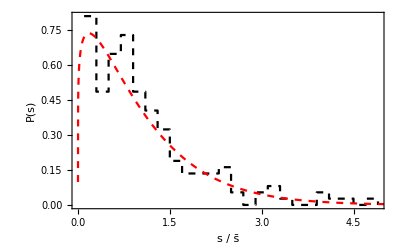

```mathematica
pcomb=Show[phistCombined,pfitCombined,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

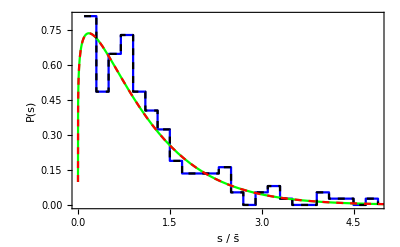

```mathematica
Show[pall3,pcomb]
```

## Run4

```mathematica
rundata4=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run4/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
80			60

LobattoPoints		NumChannels	Order
64			120		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
50.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.5d0		1.5d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff4-Ewindowsize<#<Ecutoff4-1&
curvestemp4=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run4/AdiabaticCurves.dat"]];
Curves4=Table[Table[{curvestemp4[[1,i]],curvestemp4[[j,i]]},{i,1,Length[curvestemp4[[1]]]}],{j,2,Length[curvestemp4]}];
Evals4=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs50-worse/run4/Eigenvals.dat"]];
Ecutoff4=Evals4[[4]]
Evals4=Sort[Drop[Evals4,1;;4]];
eValsBound4 = Sort[Select[Evals4,SampleRange]]
```

Ecutoff4-Ewindowsize<#1<Ecutoff4-1&

-119.733

{-149.479,-149.162,-148.658,-148.515,-148.435,-148.392,-148.318,-148.181,-147.816,-147.669,-147.625,-147.306,-147.209,-146.937,-146.808,-146.783,-146.583,-146.397,-146.239,-145.653,-145.449,-145.356,-145.197,-144.946,-144.808,-144.566,-144.493,-144.347,-144.278,-144.227,-144.041,-143.679,-143.661,-143.479,-143.468,-143.197,-142.984,-142.892,-142.571,-142.26,-142.037,-141.952,-141.709,-141.574,-141.423,-141.218,-140.922,-140.783,-140.759,-140.731,-140.552,-140.453,-140.368,-140.114,-140.041,-139.931,-139.8,-139.39,-139.292,-138.943,-138.721,-138.561,-138.463,-138.198,-138.078,-138.068,-138.002,-137.81,-137.779,-137.618,-137.52,-137.413,-137.318,-137.143,-137.005,-136.782,-136.743,-136.662,-136.532,-136.417,-136.222,-136.064,-135.617,-135.568,-135.444,-135.322,-135.166,-135.097,-135.023,-134.969,-134.731,-134.566,-134.481,-134.41,-134.322,-134.255,-134.139,-134.035,-133.948,-133.796,-133.751,-133.46,-133.32,-133.034,-132.635,-132.589,-132.51,-132.446,-132.366,-132.331,-132.259,-132.006,-131.958,-131.717,-131.611,-131.573,-131.509,-131.266,-131.225,-131.083,-131.022,-130.947,-130.904,-130.87,-130.694,-130.588,-130.518,-130.357,-130.056,-129.952,-129.788,-129.702,-129.681,-129.541,-129.301,-129.231,-129.164,-129.038,-128.985,-128.902,-128.708,-128.582,-128.54,-128.411,-128.294,-128.203,-128.049,-127.957,-127.82,-127.72,-127.65,-127.62,-127.586,-127.535,-127.52,-127.483,-127.317,-127.097,-126.976,-126.755,-126.721,-126.547,-126.499,-126.43,-126.384,-126.326,-126.157,-126.013,-125.952,-125.872,-125.739,-125.39,-125.361,-125.095,-124.999,-124.976,-124.918,-124.81,-124.77,-124.674,-124.61,-124.571,-124.467,-124.418,-124.375,-124.37,-124.329,-124.243,-124.008,-123.918,-123.839,-123.806,-123.775,-123.706,-123.66,-123.508,-123.398,-123.326,-123.221,-123.177,-123.073,-122.86,-122.653,-122.58,-122.549,-122.364,-122.334,-122.327,-122.167,-122.09,-122.014,-121.882,-121.865,-121.808,-121.704,-121.656,-121.593,-121.541,-121.465,-121.393,-121.387,-121.305,-121.243,-121.233,-121.105,-121.062,-120.929,-120.897,-120.832,-120.772}

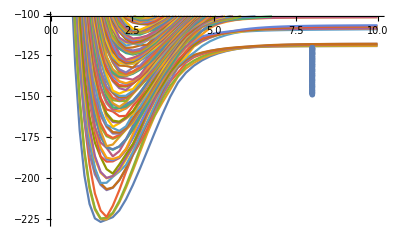

```mathematica
pcurves4=ListPlot[Curves4,Joined->True,PlotRange->{Min[curvestemp4[[2]]],Ecutoff4+18}];
penergies4=ListPlot[Table[{8,eValsBound4[[i]]},{i,1,Length[eValsBound4]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves4,penergies4]
```

```mathematica
Es4=Table[eValsBound4[[i+1]]-eValsBound4[[i]],{i,1,Length[eValsBound4]-1}];
eTrim4 = Select[Es4,#>0.0000001&];
avg4 = Mean[eTrim4];
eTrim4 = eTrim4/avg4;
Sort[eTrim4];
Length[Es4];
Length[eTrim4];
ρ4=1/avg4;
EspaceBin4=BinCounts[eTrim4,{bins}];
NormBrodyBinCs4=Table[EspaceBin4[[i]]/Total[EspaceBin4]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist4 = Table[{bFit[[i]],NormBrodyBinCs4[[i]]},{i,1,Length[bFit]}]
phist4=ListPlot[brodyPdist4,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars4 = FindFit[brodyPdist4,{PBrody[s,w],w>0,w<1},{w},s]
pfit4=Plot[PBrody[s,w/.pars4],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.283843},{0.3,0.786026},{0.5,0.786026},{0.7,0.69869},{0.9,0.436681},{1.1,0.502183},{1.3,0.393013},{1.5,0.218341},{1.7,0.218341},{1.9,0.174672},{2.1,0.131004},{2.3,0.0655022},{2.5,0.10917},{2.7,0.0436681},{2.9,0.0436681},{3.1,0.0218341},{3.3,0.0218341},{3.5,0.0218341},{3.7,0.},{3.9,0.},{4.1,0.0218341},{4.3,0.},{4.5,0.},{4.7,0.0218341},{4.9,0.}}

{w→0.462473}

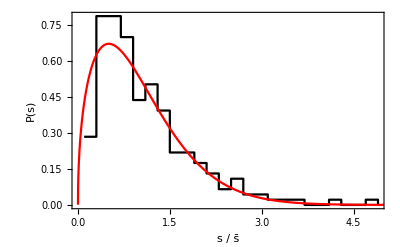

```mathematica
pall4=Show[phist4,pfit4,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

```mathematica
ρ4
```

7.97726

## We need to more closely examine the identical particle symmetries and any other symmetries in the Hamiltonian in order to understand these spectra.

We defined the Jacobi coordinates in the H-tree above so that:

(y⃗)^(12)=S_12 x⃗

where:

1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))

To keep things as general as possible I’ll assume for now that only particle 1 is of different mass and let m_2=m_3=m_4=m, and m_1=γ m  Then

μ_12=(γ m m)/(γ m+m)=mγ/(1+γ) ⟶ m/2

μ_34=m/2

μ_(12,34)=((γ m+m)(2m))/(3m+γ m)=2m(1+γ)/(3+γ)⟶ m

μ=((γ m m m m)/(γ m+3m))^(1/3)=(m(γ/(3+γ)))^(1/3) ⟶ (m/2^(2/3))

So for the equal-mass case:

2^(1/3)/(√m)(√(m/2) | -√(m/2) | 0 | 0
0 | 0 | √(m/2) | -√(m/2)
(√m)/2 | (√m)/2 | -(√m)/2 | -(√m)/2
m/(√(4m)) | m/(√(4m)) | m/(√(4m)) | m/(√(4m)))=2^(1/3)(√(1/2) | -√(1/2) | 0 | 0
0 | 0 | √(1/2) | -√(1/2)
1/2 | 1/2 | -1/2 | -1/2
1/2 | 1/2 | 1/2 | 1/2)

and

x⃗=S_12^-1(y⃗)^(12)

Then

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)

Now note that we could use the same matrix S_12 to construct (y⃗)^(13) if the matrix were to act on a column vector (x_1
x_3
x_2
x_4)  instead of the usual vector x⃗= (x_1
x_2
x_3
x_4).  We can then say:

(x_1
x_3
x_2
x_4) =(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)(x_1
x_2
x_3
x_4)=P_23 x⃗

Hence:

S_13=S_12 P_23

and

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)=S_12 P_23 S_12^-1(y⃗)^(12)

Similarly,

(y⃗)^(14)=S_14 x⃗=S_14 S_12^-1(y⃗)^(12)=S_12 P_24 S_12^-1(y⃗)^(12)

where

P_24=(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
S12=2^(1/3)({{√(1/2), -√(1/2), 0, 0}, {0, 0, √(1/2), -√(1/2)}, {1/2, 1/2, -1/2, -1/2}, {1/2, 1/2, 1/2, 1/2}});
```

```mathematica
P24=({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}});P23=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});P34=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});P14=({{0, 0, 0, 1}, {0, 1, 0, 0}, {0, 0, 1, 0}, {1, 0, 0, 0}});P13=({{0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}});P12=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
𝒫12=Simplify[S12.P12.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫12]
```

(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
𝒫34=Simplify[S12.P34.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫34]
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

```mathematica
𝒫14=Simplify[S12.P14.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫14]
```

(1/2 | -1/2 | -1/(√2)
-1/2 | 1/2 | -1/(√2)
-1/(√2) | -1/(√2) | 0)

```mathematica
𝒫13=Simplify[S12.P13.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫13]
```

(1/2 | 1/2 | -1/(√2)
1/2 | 1/2 | 1/(√2)
-1/(√2) | 1/(√2) | 0)

```mathematica
𝒫23=Simplify[S12.P23.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫23]
```

(1/2 | -1/2 | 1/(√2)
-1/2 | 1/2 | 1/(√2)
1/(√2) | 1/(√2) | 0)

```mathematica
𝒫24=Simplify[S12.P24.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫24]
```

(1/2 | 1/2 | 1/(√2)
1/2 | 1/2 | -1/(√2)
1/(√2) | -1/(√2) | 0)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14]]
```

(0 | -1 | 0
-1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫24.𝒫13]]
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14.𝒫24.𝒫13]]
```

(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

X_cm=(m_1 x_1+m_2 x_2+m_3 x_3+m_4 x_4)/(m_1+m_2+m_3+m_4)

ρ_1^(12)=x_1-x_2

ρ_2^(12)=x_3-x_4

ρ_3^(12)=(m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4)

and mass-scaled Jacobi coordinates as:

y_1^(12)=√(μ_12/μ)(x_1-x_2)

y_2^(12)=√(μ_34/μ)(x_3-x_4)

y_3^(12)=√((μ_(12,34))/μ)((m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4))

y_4^(12)=√(M/μ)X_cm

The convention here is that the superscript (12) indicates this coordinate system is convenient for treating the interaction between particles 1 and 2.  In matrix notation:

(y_1^(12)
y_2^(12)
y_3^(12)
y_4^(12))=1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))(x_1
x_2
x_3
x_4)

Now we define the hyperspherical coordinates as:

y_1^(12)=cos θ_12

y_2^(12)=sin θ_12 cos ϕ_12

y_3^(12)=sin θ_12 sin ϕ_12

```mathematica
Clear[μ4]
```

```mathematica
μ4=(μ12 μ34 μ1234)^(1/3)/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}
```

((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3)

```mathematica
A=1/(√μ4)({{√μ12, -√μ12, 0, 0}, {0, 0, √μ34, -√μ34}, {(√μ1234 m1)/(m1+m2), (√μ1234 m2)/(m1+m2), -(√μ1234 m3)/(m3+m4), -(√μ1234 m4)/(m3+m4)}, {m1/(√M), m2/(√M), m3/(√M), m4/(√M)}})/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}//FullSimplify
```

{{(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),0,0},{0,0,(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)},{(m1 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),(m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m3 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6))},{m1/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m2/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m3/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m4/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4))}}

Let’s just treat the equal mass case here...

```mathematica
({{x1}, {x2}, {x3}, {x4}})=FullSimplify[Inverse[A].({{x}, {y}, {z}, {XCM}})/.{m1->m,m2->m,m3->β m,m4->β m}];
```

```mathematica
Clear[R]
```

```mathematica
x12=Simplify[x1-x2];FullSimplify[x12,{m>0,β>0}]
x12hyp=Simplify[x12,m>0]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x12hyp,m>0]
```

(2^(1/3) x β^(1/3))/(1+β)^(1/6)

2^(1/3) R (β^2/(1+β))^(1/6) Cos[ϕ] Sin[θ]

```mathematica
x13=FullSimplify[x1-x3,{m>0,β>0}]
x13hyp=Simplify[x13]/.{x->R Sin[θ]Cos[ϕ],y-> R Sin[θ]Sin[ϕ],z-> R Cos[θ]};FullSimplify[x13hyp,{m>0,β>0}]
```

(√m x β-y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]-√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x14=FullSimplify[x1-x4,{m>0,β>0}]
x14hyp=Simplify[x14]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x14hyp,{m>0,β>0}]
```

(√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x23=Simplify[x2-x3,{m>0,β>0}]
x23hyp=Simplify[x23]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x23hyp,{m>0,β>0}]
```

-(√m x β+y √(m β)-z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]-Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x24=Simplify[x2-x4,{m>0,β>0}]
x24hyp=Simplify[x24]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x24hyp,{m>0,β>0}]
```

(-√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (-√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x34=Simplify[x3-x4,{m>0,β>0}]
x34hyp=Simplify[x3-x4,{m>0,β>0}]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x34hyp,{m>0,β>0}]
```

(2^(1/3) y)/(β (1+β))^(1/6)

(2^(1/3) R Sin[θ] Sin[ϕ])/(β (1+β))^(1/6)

```mathematica
Clear[unequalmassxij]
```

```mathematica
unequalmassxij[R_,β_]=FullSimplify[{x12hyp,x13hyp,x14hyp,x23hyp,x24hyp,x34hyp}/.{m->1,θ->t π,ϕ->f π}]
```

{2^(1/3) R (β^2/(1+β))^(1/6) Cos[f π] Sin[π t],(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]-√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-√β (√β Cos[f π]+Sin[f π]) Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(2^(1/3) R Sin[f π] Sin[π t])/((β+β^2)^(1/6))}

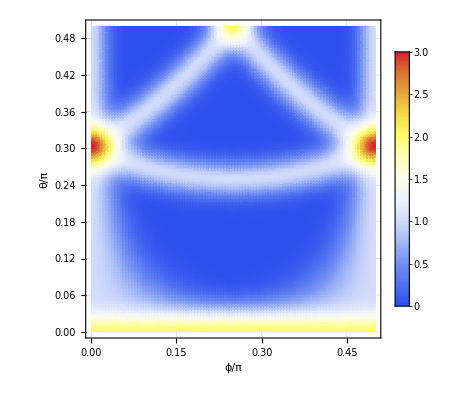

```mathematica
beta=1.0;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2],{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

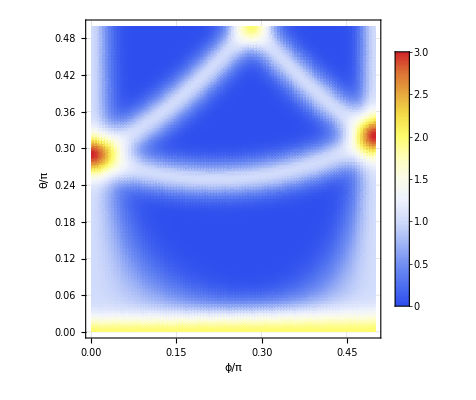

```mathematica
beta=1.5;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2]/.β->beta,{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

```mathematica
unequalmassxij[[1]]==0
```

Part::partd: Part specification unequalmassxij⟦1⟧ is longer than depth of object.

unequalmassxij⟦1⟧==0

```mathematica
c12[β_]:=ContourPlot[Evaluate[unequalmassxij[[1]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Black,FrameLabel->{"ϕ/π","θ/π"}]
c13[β_]:=ContourPlot[Evaluate[unequalmassxij[[2]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Red,FrameLabel->{"ϕ/π","θ/π"}];
c14[β_]:=ContourPlot[Evaluate[unequalmassxij[[3]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Blue,FrameLabel->{"ϕ/π","θ/π"}];
c23[β_]:=ContourPlot[Evaluate[unequalmassxij[[4]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Green,FrameLabel->{"ϕ/π","θ/π"}];
c24[β_]:=ContourPlot[Evaluate[unequalmassxij[[5]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Orange,FrameLabel->{"ϕ/π","θ/π"}];
c34[β_]:=ContourPlot[Evaluate[unequalmassxij[[6]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Yellow,FrameLabel->{"ϕ/π","θ/π"}];
```

```mathematica
c12[1.0]
```

Part::partd: Part specification unequalmassxij⟦1⟧ is longer than depth of object.

-Graphics-

Show::gcomb: Could not combine the graphics objects in Show[{c12,c13,c14,c23,c24,c34},].

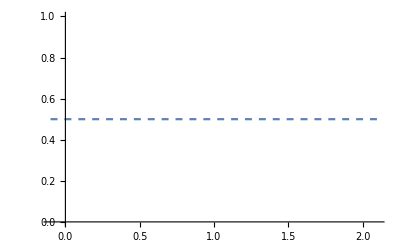
Show[{c12,c13,c14,c23,c24,c34},-Graphics-]

```mathematica
pall=Show[{c12,c13,c14,c23,c24,c34},Plot[0.5,{x,-.1,2.1},PlotStyle->Dashed]]
```

```mathematica
cptable=Table[ContourPlot[Evaluate[unequalmassxij[[i]]==0/.{R->1,α->1}],{f,0,.5},{t,0,.5},GridLines->Automatic,ContourStyle->Black],{i,1,6}];
```

Part::partd: Part specification unequalmassxij⟦1⟧ is longer than depth of object.

Part::partd: Part specification unequalmassxij⟦2⟧ is longer than depth of object.

Part::partd: Part specification unequalmassxij⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Show[pall,PlotRange->{{0,0.5},{0,0.5}}]
```

Show::gtype: Show is not a type of graphics.

Show[Show[{c12,c13,c14,c23,c24,c34},-Graphics-],PlotRange→{{0,0.5},{0,0.5}}]

### Construct a simpler model with numerical solution

Consider a 3D Hamiltonian of the form

H=ℏ^2/(2μ)∇^2 + 1/2μ r^2+k_xy x y+k_xz x z+k_yz y z

H=ℏ^2/(2μ)∇^2 + 1/2μ r^2+k_xy x y+k_xz x z+k_yz y z

Sakurai, Modern QM page 217 (translated to my preferred notation)

∫ⅆΩ Y_l^(m*)(Ω)Y_l_1^m_1(Ω)Y_l_2^m_2(Ω)=√(((2 l_1+1)(2 l_2+1))/(4π (2l+1)))l_1 0, l_2 0(l_1 l_2) l 0l_1 m_1 l_2 m_2 (l_1 l_2) l m

```mathematica
ME3[l_,m_,l1_,m1_,l2_,m2_]:=√(((2l1+1)(2l2+1))/(4π (2l+1)))ClebschGordan[{l1,0},{l2,0},{l,0}]ClebschGordan[{l1,m1},{l2,m2},{l,m}]
```

So if we need matrix elements of the form:

∫ⅆΩ Y_l^(m*)(Ω)Y_2^m_1(Ω)Y_l_2^m_2(Ω)=√((5(2 l_2+1))/(4π (2l+1)))2,0, l_2,0(l_1 l_2) l 02 m_1 l_2 m_2 (2 l_2) l m

```mathematica
Simplify[ME3[l,m,2,m1,l2,m2]]
```

Piecewise[{{1/(2 (2+l-l2) (l-l2)!)(-1)^(-3 l2+m) (1+2 l) (l^3+l^2 (1+l2)-l (2+2 l2+l2^2)-l2 (2+3 l2+l2^2)) √((5+10 l2)/(π+2 l π)) √(((2+l-l2)!)/((-1+l+l2) (l+l2) (1+l+l2) (2+l+l2) (3+l+l2) (2-l+l2)!)) ThreeJSymbol[{2,m1},{l2,m2},{l,-m}], l∈ℤ&&l2∈ℤ&&l≥0&&l2≥0&&l+l2≥2&&l2≤2+l&&l≤2+l2}, {0, True}}]

Now, since we know

x y = r^2 √(30/π)i (Y_2^-2-Y_2^2)

```mathematica
MExy[R_,l_,m_,l2_,m2_]:=R^2 ⅈ √(30/π)(ME3[l,m,2,-2,l2,m2]-ME3[l,m,2,2,l2,m2])
```

Now the issue is if we want to apply this model to test the two-component 4-fermion problem in 1D, then we need to know how to construct systematically the symmetrized 4-fermion harmonics.  We can specify the subset of harmonics by the boundary conditions implied by identical particle symmetry:

ψ(ϕ=0,θ)=ψ(ϕ=π/2,θ)=0

requires a superposition ψ~Y_l^m-(-1)^m Y_l^-m

```mathematica
Integrate[SphericalHarmonicY[lb,mb,θ,ϕ]SphericalHarmonicY[k,q,θ,ϕ]SphericalHarmonicY[lk,mk,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

$Aborted